```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"01","27"},"_"]]

c=1;
Clear[i,uu,vv,X,X1]
```

D:\Curve Elasticity\Simulation\2026\jan\results\helicoidC\alpha

01_27

```mathematica
25/26 //N
```

0.961538

```mathematica
a=0;
b=1/3;
c = 1;
X[x_]:={ x^a Cos[x], x^a Sin[x],b x};
X1[x]=X[x];

X0=D[X1[x],x];
gs=Sqrt[X0.X0] //FullSimplify;
Xs=X0/gs;
Xss=D[Xs,x]/gs  //Simplify;
g2=Sqrt[Xss.Xss] //Simplify;
L = Xss/g2;
NN = Cross[Xs,L] //Simplify;
Bs=D[NN,x]/gs  //Simplify;
kb=g2  //Simplify //N
taub=-L.Bs  //Simplify //N
```

0.9

0.3

```mathematica
(30+11x^2+x^4) //FullSimplify
```

(5+x^2) (6+x^2)

```mathematica
C1=ParametricPlot3D[X[x],{x,0,2Pi},PlotStyle->{Brown,Tube[0.051],Specularity[White,10],ViewPoint->Front},Lighting->{{"Directional",White,ImageScaled[{2,-1,2}]},{"Ambient",GrayLevel[0.4]}},Boxed->False]
```

-Graphics3D-

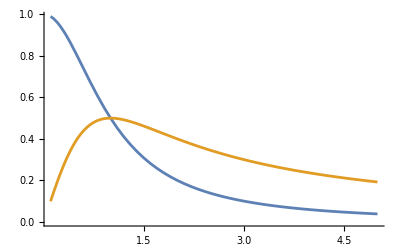

```mathematica
Plot[{kb,taub},{bb,0.1,5}]
```

```mathematica
tk=taub-kb;
dtk=D[tk,bb];
```

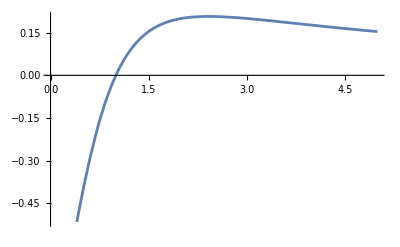

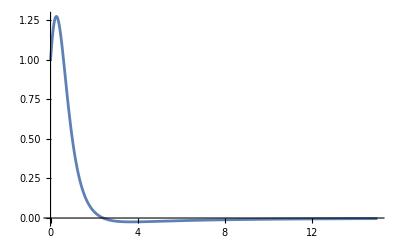

```mathematica
Plot[tk,{bb,0,5}]
Plot[{dtk},{bb,0,15},PlotRange->All]
```

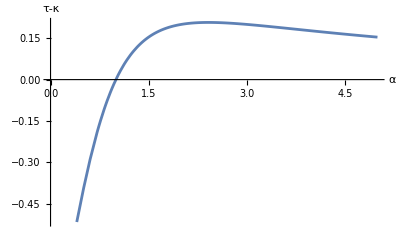

```mathematica
Show[%200,AxesLabel->{HoldForm[α],HoldForm[τ-κ]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
α
τ-κ
```

```mathematica
For[i=0,bb<5.0,bb++,
kbx[[]]=]
```

```mathematica
C1=ParametricPlot3D[X[x],{x,0,2Pi},PlotStyle->{Brown,Tube[0.1],Specularity[White,10],ViewPoint->Front},Lighting->{{"Directional",White,ImageScaled[{2,-1,2}]},{"Ambient",GrayLevel[0.4]}},Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
folder= {"0.8-0.2","0.5-0","0.5-0.5","var","st ver","st rad"};
color={Yellow,Yellow,Yellow,Yellow,Yellow,Red};
V2=Table[0,{i,1,6}];
points1=Table[0,{i,1,6}];




For[i=4,i<5,i++,

X[u_,v_]:={u Cos[v], u Sin[v],v};
uu=Import[folder[[i]]<>"\\uu_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Import[folder[[i]]<>"\\vv_2_26_"<>date<>".txt","Table"];
vv=Flatten[vv];

points=MapThread[X,{uu,vv}];
V3=ParametricPlot3D[X[u,v],{u,-1.6,1.6},{v,1,9},PlotStyle->Directive[Opacity[0.65],LightRed],MeshStyle->Directive[Opacity[0.1],GrayLevel[0.]]];

V2[[i]]=Graphics3D[{color[[i]],Tube[points,0.1],Black,Sphere[X[uu[[2001]],vv[[2001]]],0.15]},Lighting->{{"Directional",White,ImageScaled[{1,-1,2}]},{"Ambient",GrayLevel[0.25]}},PlotRange->All,Axes->True]; ]
```

```mathematica
i=4;
as=Show[V3,V2[[i]],Axes->{False,True,True},AxesLabel->{Style["x",Bold,Italic,16],Style["y",Bold,Italic,16],Style["z",Bold,Italic,16]},TicksStyle->Directive[Black, Bold,10],Boxed->False, ViewPoint->Right,Frame->True,Boxed->False];
C1 =Show[C1,Axes->{False,True,True},AxesLabel->{Style["x",Bold,Italic,16],Style["y",Bold,Italic,16],Style["z",Bold,Italic,16]},TicksStyle->Directive[Black, Bold,10],Boxed->False, ViewPoint->Right,Frame->True,Boxed->False];
a1=GraphicsRow[{C1,as}]

as2=Show[V3,V2[[i]],Axes->{True,True,False},AxesLabel->{Style["x",Bold,Italic,16],Style["y",Bold,Italic,16],Style["z",Bold,Italic,16]},TicksStyle->Directive[Black, Bold,10],Boxed->False,ViewPoint->Above,Axes->True,Boxed->False];
C2 =Show[C1,Axes->{True,True,False},AxesLabel->{Style["x",Bold,Italic,16],Style["y",Bold,Italic,16],Style["z",Bold,Italic,16]},TicksStyle->Directive[Black, Bold,10],Boxed->False,ViewPoint->Above,Axes->True,Boxed->False];
a2=GraphicsRow[{C2,as2}];

as3=Show[V3,V2[[i]],Axes->False,PlotRange->Automatic,Boxed->False, ViewPoint->{4,-4, 3},Frame->True,Boxed->False];
C3 =Show[C1,Axes->False,Boxed->False, ViewPoint->{4,-3, 3},Frame->True,Boxed->False];
a3=GraphicsRow[{C3,as3}];
```

-Graphics-

```mathematica
aF=GraphicsColumn[{a1,a2,a3},AspectRatio->Automatic];
Export["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\helicoidC\\images\\var.png",aF,"PNG"]
```

D:\Curve Elasticity\Simulation\2026\jan\results\helicoidC\images\var.png

```mathematica
Export["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\helicoidC\\images\\var.eps",aF,"eps"]
```

D:\Curve Elasticity\Simulation\2026\jan\results\helicoidC\images\var.eps